## Study the wobbling quantities for 136Nd

```mathematica
ClearAll["Global`*"]
```

```mathematica
ZZ=60;
AA=136;
```

### Fitting parameters

The “lower” structure has two wobbling bands (n=0,1)
The “higher” structure was three wobbling bands (n=0,1,2)

```mathematica
moi[x_]:=1/(2*x);
bandhead=10;
A1higher=0.014062276282211794;
A2higher=0.013302239436739938;
A3higher=0.012775354285838508;
A1lower=0.02295303019867904;
A2lower=0.022180318456442378;
A3lower=0.015060621351560706;
I1lower=moi[A1lower];
I2lower=moi[A2lower];
I3lower=moi[A3lower];
I1higher=moi[A1higher];
I2higher=moi[A2higher];
I3higher=moi[A3higher];
```

```mathematica
spins1higher={12,14,16,18,20,22};
spins2higher={13,15,17,19,21};
spins3higher={14,16,18,20,22,24};
energy1higher={0.39,1.051,1.895,2.894,4.055,5.321};
energy2higher={1.158,1.836,2.646,3.634,4.804};
energy3higher={1.559,2.274,3.176,4.035,4.928,5.877};
spins1lower={12,14,16};
spins2lower={11,13,15};
energy1lower={0.718,1.57,2.564};
energy2lower={0.749,1.268,2.069};
```

### Theoretical formalism

```mathematica
omega[I_,A1_,A2_,A3_]:=2I*Sqrt[(A1-A3)(A2-A3)];
En[I_,n_,A1_,A2_,A3_]:=A3*I*(I+1)+omega[I,A1,A2,A3]*(n+1/2);
Exc[I_,n_,A1_,A2_,A3_]:=En[I,n,A1,A2,A3]-En[bandhead,0,A1,A2,A3];
```

```mathematica
data1higherExp=Table[{spins1higher[[i]],energy1higher[[i]]},{i,1,Length[spins1higher]}];
data2higherExp=Table[{spins2higher[[i]],energy2higher[[i]]},{i,1,Length[spins2higher]}];
data3higherExp=Table[{spins3higher[[i]],energy3higher[[i]]},{i,1,Length[spins3higher]}];
data1higherTh=Table[{spins1higher[[i]],Exc[spins1higher[[i]],0,A1higher,A2higher,A3higher]},{i,1,Length[spins1higher]}];
data2higherTh=Table[{spins2higher[[i]],Exc[spins2higher[[i]],1,A1higher,A2higher,A3higher]},{i,1,Length[spins2higher]}];
data3higherTh=Table[{spins3higher[[i]],Exc[spins3higher[[i]],2,A1higher,A2higher,A3higher]},{i,1,Length[spins3higher]}];
data1lowerExp=Table[{spins1lower[[i]],energy1lower[[i]]},{i,1,Length[spins1lower]}];
data2lowerExp=Table[{spins2lower[[i]],energy2lower[[i]]},{i,1,Length[spins2lower]}];
data1lowerTh=Table[{spins1lower[[i]],Exc[spins1lower[[i]],0,A1lower,A2lower,A3lower]},{i,1,Length[spins1lower]}];
data2lowerTh=Table[{spins2lower[[i]],Exc[spins2lower[[i]],1,A1lower,A2lower,A3lower]},{i,1,Length[spins2lower]}];
```

```mathematica
Sqrt[1/(Length[data1lowerExp]+Length[data2lowerExp])*(Sum[(data1lowerExp[[i,2]]-data1lowerTh[[i,2]])^2/data1lowerExp[[i,2]],{i,1,Length[data1lowerExp]}]+Sum[(data2lowerExp[[i,2]]-data2lowerTh[[i,2]])^2/data2lowerExp[[i,2]],{i,1,Length[data2lowerExp]}])]
Sqrt[1/(Length[data1higherExp]+Length[data2higherExp]+Length[data3higherExp])*(Sum[(data1higherExp[[i,2]]-data1higherTh[[i,2]])^2/data1higherExp[[i,2]],{i,1,Length[data1higherExp]}]+Sum[(data2higherExp[[i,2]]-data2higherTh[[i,2]])^2/data2higherExp[[i,2]],{i,1,Length[data2higherExp]}]+Sum[(data3higherExp[[i,2]]-data3higherTh[[i,2]])^2/data3higherExp[[i,2]],{i,1,Length[data3higherExp]}])]
```

0.12622

0.145347

### Graphical representations

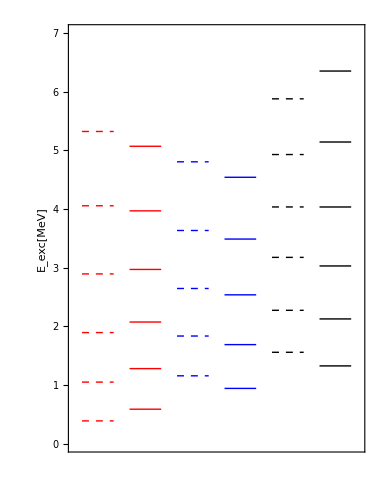

```mathematica
band1higherExp=ListLinePlot[Table[{{1,data1higherExp[[i,2]]},{3,data1higherExp[[i,2]]}},{i,1,Length[data1higherExp]}],PlotStyle->Directive[Red,Dashed,Thick],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,Automatic},{None,None}},LabelStyle->{20,Bold,Black,FontFamily->"Times"},FrameLabel->{None,"E_exc[MeV]"},ImageSize->380];
band1higherTh=ListLinePlot[Table[{{4,data1higherTh[[i,2]]},{6,data1higherTh[[i,2]]}},{i,1,Length[data1higherTh]}],PlotStyle->Directive[Red,Thick]];
band2higherExp=ListLinePlot[Table[{{7,data2higherExp[[i,2]]},{9,data2higherExp[[i,2]]}},{i,1,Length[data2higherExp]}],PlotStyle->Directive[Blue,Dashed,Thick]];
band2higherTh=ListLinePlot[Table[{{10,data2higherTh[[i,2]]},{12,data2higherTh[[i,2]]}},{i,1,Length[data2higherTh]}],PlotStyle->Directive[Blue,Thick]];
band3higherExp=ListLinePlot[Table[{{13,data3higherExp[[i,2]]},{15,data3higherExp[[i,2]]}},{i,1,Length[data3higherExp]}],PlotStyle->Directive[Black,Dashed,Thick]];
band3higherTh=ListLinePlot[Table[{{16,data3higherTh[[i,2]]},{18,data3higherTh[[i,2]]}},{i,1,Length[data3higherTh]}],PlotStyle->Directive[Black,Thick]];
obj1=Show[{band1higherExp,band1higherTh,band2higherExp,band2higherTh,band3higherExp,band3higherTh},AspectRatio->1.3,PlotRange->{{0.5,18.5},{0,7}}];
Show[obj1]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/136Nd-excitation-higher.pdf",Show[obj1]];
```

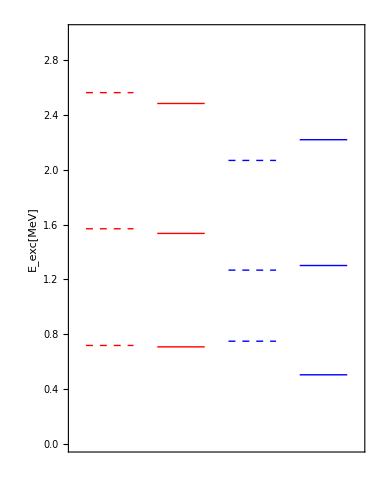

{{{},{},{0,1/2 √((-Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Thickness[Large]]+Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Dashing[{Small,Small}],Thickness[Large]])^2/Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Dashing[{Small,Small}],Thickness[Large]]+(-Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Thickness[Large]]+Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Dashing[{Small,Small}],Thickness[Large]])^2/Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Dashing[{Small,Small}],Thickness[Large]]),1/2 √((Line[{{1.,0.718},{3.,0.718},{3.,0.718}}]-Line[{{4.,0.707781},{6.,0.707781},{6.,0.707781}}])^2/Line[{{1.,0.718},{3.,0.718},{3.,0.718}}]+(Line[{{7.,0.749},{9.,0.749},{9.,0.749}}]-Line[{{10.,0.503744},{12.,0.503744},{12.,0.503744}}])^2/Line[{{7.,0.749},{9.,0.749},{9.,0.749}}])},{0,1/2 √((-Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Thickness[Large]]+Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Dashing[{Small,Small}],Thickness[Large]])^2/Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Dashing[{Small,Small}],Thickness[Large]]+(-Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Thickness[Large]]+Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Dashing[{Small,Small}],Thickness[Large]])^2/Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Dashing[{Small,Small}],Thickness[Large]]),1/2 √((Line[{{1.,1.57},{3.,1.57},{3.,1.57}}]-Line[{{4.,1.53605},{6.,1.53605},{6.,1.53605}}])^2/Line[{{1.,1.57},{3.,1.57},{3.,1.57}}]+(Line[{{7.,1.268},{9.,1.268},{9.,1.268}}]-Line[{{10.,1.30175},{12.,1.30175},{12.,1.30175}}])^2/Line[{{7.,1.268},{9.,1.268},{9.,1.268}}])},{0,1/2 √((-Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Thickness[Large]]+Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Dashing[{Small,Small}],Thickness[Large]])^2/Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[0, 0, 1],Dashing[{Small,Small}],Thickness[Large]]+(-Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Thickness[Large]]+Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Dashing[{Small,Small}],Thickness[Large]])^2/Directive[PointSize[7/360],AbsoluteThickness[1.6],RGBColor[1, 0, 0],Dashing[{Small,Small}],Thickness[Large]]),1/2 √((Line[{{1.,2.564},{3.,2.564},{3.,2.564}}]-Line[{{4.,2.4848},{6.,2.4848},{6.,2.4848}}])^2/Line[{{1.,2.564},{3.,2.564},{3.,2.564}}]+(Line[{{7.,2.069},{9.,2.069},{9.,2.069}}]-Line[{{10.,2.22024},{12.,2.22024},{12.,2.22024}}])^2/Line[{{7.,2.069},{9.,2.069},{9.,2.069}}])}}}

```mathematica
band1lowerExp=ListLinePlot[Table[{{1,data1lowerExp[[i,2]]},{3,data1lowerExp[[i,2]]}},{i,1,Length[data1lowerExp]}],PlotStyle->Directive[Red,Dashed,Thick],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,Automatic},{None,None}},LabelStyle->{20,Bold,Black,FontFamily->"Times"},FrameLabel->{None,"E_exc[MeV]"},ImageSize->380];
band1lowerTh=ListLinePlot[Table[{{4,data1lowerTh[[i,2]]},{6,data1lowerTh[[i,2]]}},{i,1,Length[data1lowerTh]}],PlotStyle->Directive[Red,Thick]];
band2lowerExp=ListLinePlot[Table[{{7,data2lowerExp[[i,2]]},{9,data2lowerExp[[i,2]]}},{i,1,Length[data2lowerExp]}],PlotStyle->Directive[Blue,Dashed,Thick]];
band2lowerTh=ListLinePlot[Table[{{10,data2lowerTh[[i,2]]},{12,data2lowerTh[[i,2]]}},{i,1,Length[data2lowerTh]}],PlotStyle->Directive[Blue,Thick]];
obj2=Show[{band1lowerExp,band1lowerTh,band2lowerExp,band2lowerTh},AspectRatio->1.3,PlotRange->{{0.5,12.5},{0,3}}];
Show[obj2]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/136Nd-excitation-lower.pdf",Show[obj2]];
```

## Electromagnetic transitions

```mathematica
t1[I_,A1_,A2_,A3_]:=I(A2+A1-2A3);
t2[I_,A1_,A2_]:=I(A2-A1);
w1[I_,A1_,A2_,A3_]:=(1/2(t1[I,A1,A2,A3]/(√(t1[I,A1,A2,A3]^2-t2[I,A1,A2]^2))+1))^(1/2);
w2[I_,A1_,A2_,A3_]:=(1/2(t1[I,A1,A2,A3]/(√(t1[I,A1,A2,A3]^2-t2[I,A1,A2]^2))-1))^(1/2);
Q0def[A_,Z_,beta_]:=3/(√(5π))(1.2*A^(1/3))^2*Z*beta*(1+0.16*beta);
Q20[Q0_,gm_]:=Q0*Cos[gm];
Q22[Q0_,gm_]:=1/(√2)Q0*Sin[gm];
BE2out[I_,n_,Q0_,gm_,A1_,A2_,A3_]:=5/(16π)*n/I(√3 Q20[Q0,gm]*w1[I,A1,A2,A3]+√2 Q22[Q0,gm]*w2[I,A1,A2,A3])^2;
BE2in[I_,Q0_,gm_]:=5/(16π)*Q22[Q0,gm]^2;
quench1=10^-4/2;
quench2=quench1*10;
```

## Higher

```mathematica
gmhigher=25*π/180;
beta2higher=0.20/0.95;
w1higher=w1[1,A1higher,A2higher,A3higher];
w2higher=w2[1,A1higher,A2higher,A3higher];
Q0higher=Q0def[AA,ZZ,beta2higher];
Q20higher=Q20[Q0higher,gmhigher];
Q22higher=Q22[Q0higher,gmhigher];
BE2inhigher=BE2in[1,Q0higher,gmhigher]*quench2;
```

## Lower

```mathematica
gmlower=-35*π/180;
beta2lower=0.15/0.95;
w1lower=w1[1,A1lower,A2lower,A3lower];
w2lower=w2[1,A1lower,A2lower,A3lower];
Q0lower=Q0def[AA,ZZ,beta2lower];
Q20lower=Q20[Q0lower,gmlower];
Q22lower=Q22[Q0lower,gmlower];
BE2inlower=BE2in[1,Q0lower,gmlower]*quench2;
```

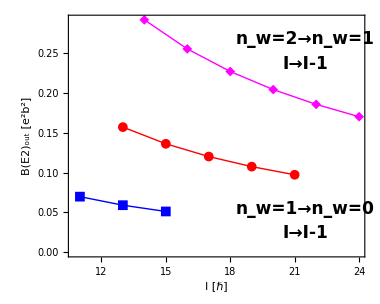

```mathematica
BE2outPlot=ListPlot[{Table[{spins2higher[[i]],quench1*BE2out[spins2higher[[i]],1,Q0higher,gmhigher,A1higher,A2higher,A3higher]},{i,1,Length[spins2higher]}],Table[{spins2lower[[i]],quench1*BE2out[spins2lower[[i]],1,Q0lower,gmlower,A1lower,A2lower,A3lower]},{i,1,Length[spins2lower]}],Table[{spins3higher[[i]],quench1*BE2out[spins3higher[[i]],2,Q0higher,gmhigher,A1higher,A2higher,A3higher]},{i,1,Length[spins3higher]}]},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True,True},PlotStyle->{{Red,Thick},{Blue,Thick},{Magenta,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","B(E2)_out [e^2b^2]"},PlotMarkers->{Automatic, Medium},Epilog->{Inset[Style["n_w=1→n_w=0",Bold,17,Black],Scaled[{0.8,0.2}]],Inset[Style["I→I-1",Bold,Italic,17,Black],Scaled[{0.8,0.1}]],Inset[Style["n_w=2→n_w=1",Bold,17,Black],Scaled[{0.8,0.9}]],Inset[Style["I→I-1",Bold,Italic,17,Black],Scaled[{0.8,0.8}]]},PlotRange->Full];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/136Nd-BE2-out.pdf",BE2outPlot];
Show[BE2outPlot]
```

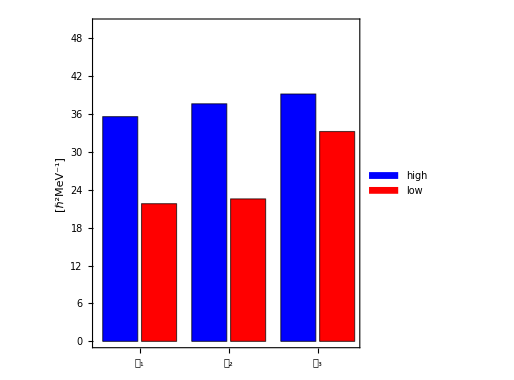

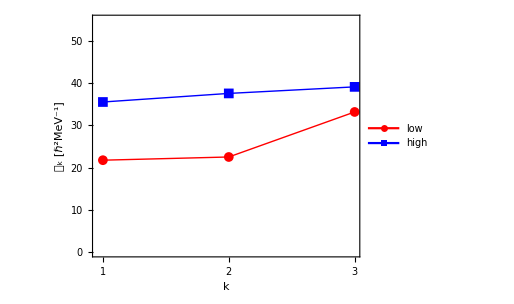

```mathematica
mois2=BarChart[{{I1higher,I1lower},{I2higher,I2lower},{I3higher,I3lower}},ChartLabels->{{"𝒥_1","𝒥_2","𝒥_3"},None},AspectRatio->1,ChartLegends->{"high","low"},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{None,"[ℏ^2MeV^-1]"},ChartStyle->{Blue,Red},PlotRange->{0,50}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/136Nd-mois-bars.pdf",mois2];
Show[mois2]
moiplot=ListPlot[{{{1,I1lower},{2,I2lower},{3,I3lower}},{{1,I1higher},{2,I2higher},{3,I3higher}}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"low","high"},{0.25,0.8}],FrameLabel->{"k","𝒥_k [ℏ^2MeV^-1]"},PlotMarkers->{Automatic, Medium},PlotRange->{Automatic,{0,55}},FrameTicks->{{Automatic,None},{{1,2,3},None}}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/136Nd-mois.pdf",moiplot];
Show[moiplot]
```